```mathematica
Needs["HierarchicalClustering`"]
SetOptions[{Plot,MatrixPlot},ImageSize->250{1,1}];
```

An exercise in the damping parameter, δ y’[t] introduced into the traditional Duffing oscillator, viz., μ y’’ + y + ϵ y^3 = f(T1,T2).  f(T1,T2) is a multi mode signal.  The damping parameter when introduced with a non-zero δ (such as δ=1.0), leads to the removal of one of the modes in the multimode signal.  The nearness parameter, nn, in the recurrence plot section may be changed.  A larger value of nn suggests the tabulation of a recurrence of the oscillator trajectory within nn*100 (%) of any previous position.  “Techniqually, the RP reveals all the times when the phase space trajectory of the dynamical system visits roughly the same area in the phase space.”  “Floral structures” in a recurrence plot result from superpositioned harmonic oscillations.

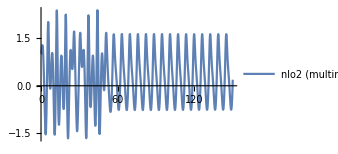
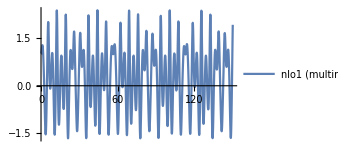
-Graphics- -Graphics- -Graphics- -Graphics-

```mathematica
Module[{tmax=150,ϵ=1,δ,δ2,γ=2,μ=1,T1,T2,T3,nlo1,nlo2},
δ=0;
nlo1=NDSolveValue[{μ y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==1+γ Cos[t/1000]Cos[t/1],y[0]==1,y'[0]==0},y,{t,0,tmax}];
nlo2=NDSolveValue[{μ y''[t]+δ2[t] y'[t]+y[t]+ϵ (y[t])^3==1+γ Cos[t/1000]Cos[t/1],y[0]==1,y'[0]==0,δ2[0]==0.,WhenEvent[t>50,δ2[t]->1]},y,{t,0,tmax},DiscreteVariables->δ2];
Plot[{nlo1[t]},{t,0,tmax},PlotLegends->{"nlo1 (multimode)"}]
Plot[{nlo2[t]},{t,0,tmax},PlotLegends->{"nlo2 (multimode with δ=1 intro'd at t>50)"}]

(*Recurrence plots are calculated*)
With[{stepSize=0.2,end=tmax,nn=0.05},
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo1[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]

MatrixPlot[UnitStep[nn-DistanceMatrix[nlo2[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]
]
]
```

Superpositioned harmonic oscillations as shown in a recurrence plot.  The same Duffing oscillator is chosen (without damping).  The time of simulation is shortened so as to capture tesellated RP patterns more clearly.  The forcing function is still multimode but with the two modes of not extremely disparate time periods, T1, T2. i.e., instead of 1+γ Cos[t/1000]Cos[t/1], now, 1+γ Cos[t/10]Cos[t/1] is chosen instead.  This results in a floral pattern.

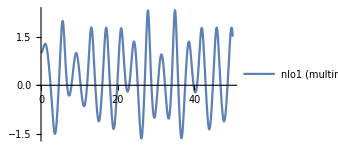
-Graphics- -Graphics-

```mathematica
Module[{tmax=50,ϵ=1,δ,δ2,γ=2,μ=1,T1,T2,T3,nlo1,nlo2},
δ=0;
nlo1=NDSolveValue[{μ y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==1+γ Cos[t/10]Cos[t/1],y[0]==1,y'[0]==0},y,{t,0,tmax}];

Plot[{nlo1[t]},{t,0,tmax},PlotLegends->{"nlo1 (multimode)"}]

(*Recurrence plots are calculated*)
With[{stepSize=0.2,end=tmax,nn=0.05},
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo1[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]
]
]
```